```mathematica
Needs["NDSolve`FEM`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
ClearAll[aux,ARR1,PLT,length,auxinDiff,plethora]

ourParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, aux] ->600, Subscript[D, PLT]->550,Subscript[P, PIN]-> 0.1};
paramsPaper={k1-> 0,k2->1,k3-> -1,k4-> -1.59,k5-> -0.1,k6->0, k7->-1.27, k8->0,k9->-0.1, Subscript[D, PLT]->2.5,Subscript[D, aux] ->1};
paramsvaryPIN={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, PLT]-> 550,Subscript[D, ARR1]->0, Subscript[D, aux] ->600,j0A-> 10^-5};
paramsvaryD={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,j0A-> 10^-3};
paramsvaryPINvaryD={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,Subscript[D, ARR1] -> 0 ,j0A-> 10^-3};
NDParams={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1 ,d-> 1,j0A-> 10^-3,Pe->2,γ-> 1000};
paramsNDvaryPINvaryD={k1->0,k2->-1.98,k3->1,k4-> -0.48,k5-> 0,k6->0, k7->-1, k8->0.2,k9->-0.1,j0A-> 10^-3};



arr1={D[ARR1[x,t],t]==k1 *ARR1[x,t]+ k2 *PLT[x,t]+k3*aux[x,t] +alpha-(ARR1[x,t])^3+Subscript[D, ARR1]*D[ARR1[x,t],x,x]};
plethora={D[PLT[x,t],t]==k4  *ARR1[x,t]+k5 *PLT[x,t]+k6 * aux[x,t]+beta+Subscript[D, PLT]*D[PLT[x,t],x,x]}
auxinDiff={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]}
auxinAdvUnifTransp={D[aux[x,t],t]==k7 *ARR1[x,t] +k8 *PLT[x,t]+k9  * aux[x,t]+gamma+Subscript[D, aux]*D[aux[x,t],x,x]+Subscript[P, PIN]*D[aux[x,t],x]};
ic = {ARR1[x,t]==-0.2/.t->0,PLT[x,t]==-0.1/.t->0,aux[x,t]==-0.1/.t->0};

bcDifflong= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0A/.x->lengtlong,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->lengtlong,ARR1[x,t]==-0.2/.x->0,ARR1[x,t]==-0.2/.x->lengtlong};
bcDiffshort= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==0/.x->lengthshort,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->lengthshort,ARR1[x,t]==0/.x->0,ARR1[x,t]==0/.x->lengthshort};

bcAdvlong= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0A/.x->lengtlong,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->lengtlong,ARR1[0,t]==-0.1, ARR1[lengtlong,t]==-0.1};
bcAdvshort= {D[aux[x,t],x]==0/.x->0,D[aux[x,t],x]==j0A/.x->lengthshort,D[PLT[x,t],x]==0/.x->0,D[PLT[x,t],x]==0/.x->lengthshort,ARR1[0,t]==-0.1, ARR1[lengthshort,t]==-0.1};

tFinal = 10000;
PINvary= Table[i,{i,0.01,0.1,0.02}]
PINvaryMZ[x]=Table[ Piecewise[{{i,0≤x≤200}},0],{i,0.07,0.2,0.05}]

Subscript[P, PIN][x,t]:=Piecewise[{{2,0≤x≤200}},0]


Building the set of pdes for each case

pdesDiff = {arr1,plethora,auxinDiff};
pdesAdvUnif = {arr1,plethora,auxinAdvUnifTransp};
lengtlong=500;
lengthshort=100;

tFinal = 10000;

DPLTvarylong = Table[i,{i,300,600,50}]
Dauxvarylong = Table[i,{i,100,600,50}]

DPLTvaryshort = Table[i,{i,7,10,0.5}]
Dauxvaryshort = Table[i,{i,1,10,2}]
Subscript[P, PIN][x,t]:=Piecewise[{{2,0≤x≤200}},0]

Parameter space variation
```

{PLT^(0,1)[x,t]==beta+k4 ARR1[x,t]+k6 aux[x,t]+k5 PLT[x,t]+D_PLT PLT^(2,0)[x,t]}

{aux^(0,1)[x,t]==gamma+k7 ARR1[x,t]+k9 aux[x,t]+k8 PLT[x,t]+D_aux aux^(2,0)[x,t]}

{0.01,0.03,0.05,0.07,0.09}

{Piecewise[{{0.07, 0≤x≤200}, {0, True}}],Piecewise[{{0.12, 0≤x≤200}, {0, True}}],Piecewise[{{0.17, 0≤x≤200}, {0, True}}]}

Building case each for of pdes set the

{300,350,400,450,500,550,600}

{100,150,200,250,300,350,400,450,500,550,600}

{7.,7.5,8.,8.5,9.,9.5,10.}

{1,3,5,7,9}

Parameter space variation

```mathematica
I.a Varying PIN strength values
solUnifbutVaryPIN=Table[NDSolve[Flatten@{pdesAdvUnif,ic,bcAdvlong}/.Subscript[P, PIN]->Pval/.paramsvaryPIN/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,lengtlong},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}},PrecisionGoal->2],{Pval,PINvary}];
```

PIN strength values Varying ⅈ.a

```mathematica
Length[solUnifbutVaryPIN]
```

10

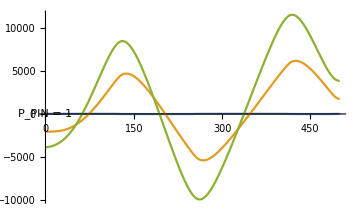
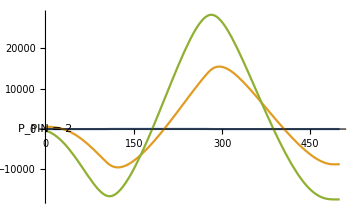
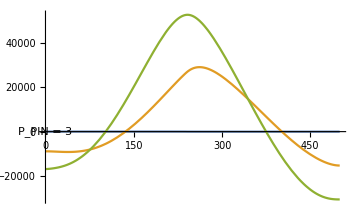
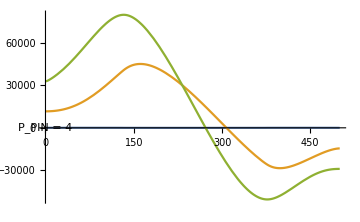
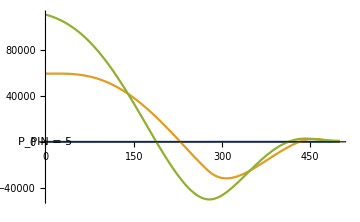
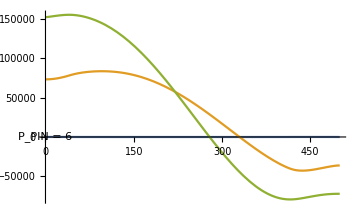
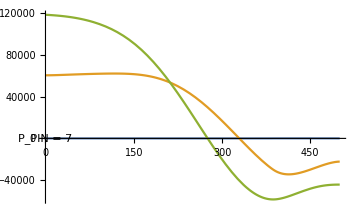
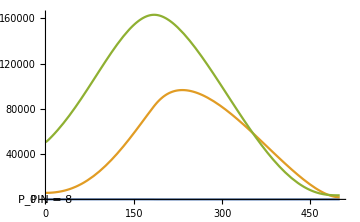

```mathematica
plotUnifbutVaryPIN=Flatten@Table[Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solUnifbutVaryPIN⟦index⟧/.t->tFinal],{x,0,lengtlong},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["P_PIN = "<>ToString[PINvary⟦index⟧]],RoundingRadius->5]]}],{index,1,Length[PINvary],1}]
```

```mathematica
II.a Varying PINs in MZ
solUnifbutVaryPINMZ=Table[NDSolve[Flatten@{pdesAdvUnif,ic,bcAdv}/.Subscript[P, PIN]->Pval/.paramsvaryPIN/.alpha-> 0/.beta-> 0/.gamma->0,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200}},PrecisionGoal->2],{Pval,PINvaryMZ[x]}];


plotUnifbutVaryPINMZ=Flatten@Table[Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solUnifbutVaryPINMZ⟦index⟧/.t->tFinal],{x,0,length},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["P_PIN = "<>ToString[PINvaryMZ[x]⟦index⟧]],RoundingRadius->5]]}],{index,1,Length[PINvaryMZ[x]],1}];

Comparing the resulting profile in unif PIN parameter space vs diff only
ncol=2;

Table[Grid[Partition[{plotUnifbutVaryPINMZ[[i]],plotUnifbutVaryPIN[[i]]},ncol]],{i,1,Length[plotUnifbutVaryPIN]}]
```

```mathematica
Comparing the resulting profile in unif PIN parameter space vs PINs in MZ
```

```mathematica
ncol=2
2
Table[Grid[Partition[{plotUnifbutVaryPINMZ[[i]],plotUnifbutVaryPIN[[i]]},ncol]],{i,1,Length[plotUnifbutVaryPIN]}]
```

```mathematica
Varying diffusion coefficients-Only diff
```

#### Long length

```mathematica
solvevaryDiffprovalong=Table[NDSolve[Flatten@{pdesDiff,ic,bcDifflong}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, aux]-> auxval/.Subscript[D, PLT]-> PLTval/.Subscript[D, ARR1]-> 0,{ARR1,PLT,aux},{x,0,lengtlong},{t,0,1000},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1000}} ,PrecisionGoal->2],{auxval,Dauxvarylong},{PLTval,DPLTvarylong}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

```mathematica
plotvarydiffprovalong=Flatten@Table[Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solvevaryDiffprovalong⟦i,j⟧/.t->1000],{x,0,lengtlong},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["Daux = "<>ToString[Dauxvarylong⟦i⟧]<>", Dplt = "<>ToString[DPLTvarylong⟦j⟧]],RoundingRadius->5]]}],{i,1,Length[Dauxvarylong],1},{j,1,Length[DPLTvarylong],1}]
```

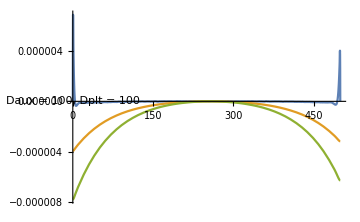
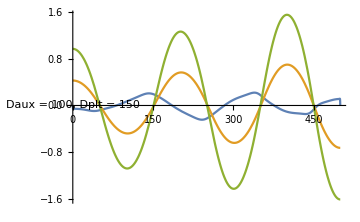
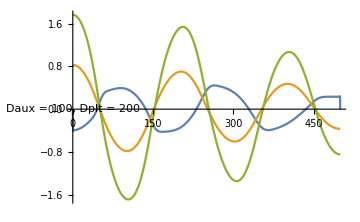
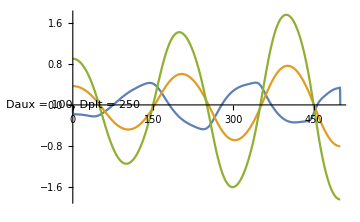
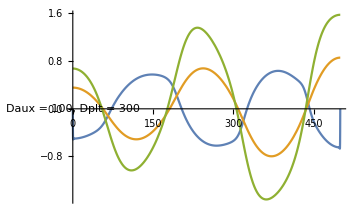
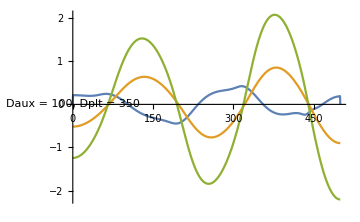
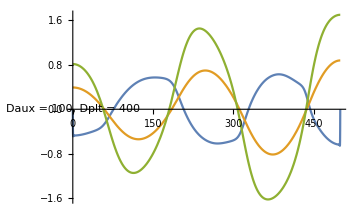
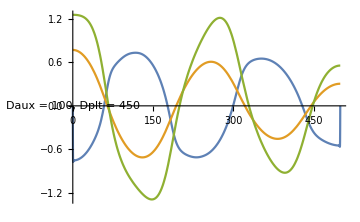
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

#### Short length

```mathematica
solvevaryDiffprovashort=Table[NDSolve[Flatten@{pdesDiff,ic,bcDiffshort}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, aux]-> auxval/.Subscript[D, PLT]-> PLTval/.Subscript[D, ARR1]-> 0,{ARR1,PLT,aux},{x,0,lengthshort},{t,0,1000},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1000}} ,PrecisionGoal->2],{auxval,Dauxvaryshort},{PLTval,DPLTvaryshort}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

```mathematica
plotvarydiffprovashort=Flatten@Table[Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solvevaryDiffprovashort⟦i,j⟧/.t->1000],{x,0,lengthshort},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["Daux = "<>ToString[Dauxvaryshort⟦i⟧]<>", Dplt = "<>ToString[DPLTvaryshort⟦j⟧]],RoundingRadius->5]]}],{i,1,Length[Dauxvaryshort],1},{j,1,Length[DPLTvaryshort],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
solveDiff=NDSolve[{pdesDiff,ic,bcDifflong}/.ourParams/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, ARR1]-> 0,{ARR1,PLT,aux},{x,0,lengtlong},{t,0,1000},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->1000}} ,PrecisionGoal->2]

solveplotDiff= Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solveDiff[[1]]/.t->1000],{x,0,lengtlong},PlotRange->All,PlotLegends->{ARR1,PLT,aux},PlotLabel->ToString[pdesDiff,TraditionalForm],BaseStyle->{FontWeight->"Bold",FontSize->7},ImageSize->Large]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{ARR1→InterpolatingFunction[{{0., 500.}, {0., 1000.}}, <>],PLT→InterpolatingFunction[{{0., 500.}, {0., 1000.}}, <>],aux→InterpolatingFunction[{{0., 500.}, {0., 1000.}}, <>]}}

-Graphics-

```mathematica
Varying both diff.and PINs-PIN uniform- long length
solvevaryDiffPINuniflong=Table[NDSolve[Flatten@{pdesAdvUnif,ic,bcAdvlong}/.paramsvaryPINvaryD/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, aux]->600/.Subscript[D, PLT]->PLTval/.Subscript[P, PIN]-> Pval,{ARR1,PLT,aux},{x,0,lengtlong},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}} ,PrecisionGoal->2],{PLTval,DPLTvarylong},{Pval,PINvary}];

plotvarydiffPINuniflong=Flatten@Table[Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solvevaryDiffPINuniflong⟦i,j⟧/.t->tFinal],{x,0,lengtlong},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["Dplt= "<>ToString[DPLTvarylong⟦i⟧]<>", PIN= "<>ToString[PINvary⟦j⟧]],RoundingRadius->5]]}],{i,1,Length[DPLTvarylong],1},{j,1,Length[PINvary],1}]
```

-length long-PIN uniform+both PINs Varying diff.and

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Varying both diff.and PINs-PIN uniform -short length
solvevaryDiffPINunifshort=Table[NDSolve[Flatten@{pdesAdvUnif,ic,bcAdvshort}/.paramsvaryPINvaryD/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, aux]->10/.Subscript[D, PLT]->PLTval/.Subscript[P, PIN]-> Pval,{ARR1,PLT,aux},{x,0,lengthshort},{t,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}} ,PrecisionGoal->2],{PLTval,DPLTvaryshort},{Pval,PINvary}];

plotvarydiffPINunifshort=Flatten@Table[Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solvevaryDiffPINunifshort⟦i,j⟧/.t->tFinal],{x,0,lengthshort},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["Dplt= "<>ToString[DPLTvaryshort⟦i⟧]<>", PIN= "<>ToString[PINvary⟦j⟧]],RoundingRadius->5]]}],{i,1,Length[DPLTvaryshort],1},{j,1,Length[PINvary],1}]
```

-length short-PIN uniform+both PINs Varying diff.and

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Varying both diff.and PINs-PIN only in MZ
solvevaryDiffPINonlyMZ=Table[NDSolve[Flatten@{pdesAdvOnlyMZ,ic,bcAdv}/.paramsvaryPINvaryD/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, aux]-> 100/.Subscript[D, PLT]-> PLTval/.Subscript[P, PIN]-> Pval,{ARR1,PLT,aux},{x,0,length},{t,0,tFinal}(*,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->150}}*) ,PrecisionGoal->2],{PLTval,DPLTvary},{Pval,PINvaryMZ[x]}];

plotvarydiffPINonlyMZ=Flatten@Table[Plot[Evaluate[{aux[x,t],PLT[x,t],ARR1[x,t]}/.solvevaryDiffPINonlyMZ⟦i,j⟧/.t->tFinal],{x,0,length},PlotRange->All,ImageSize->Medium,Epilog->{Inset[Framed[Text["DPLT= "<>ToString[DPLTvary⟦i⟧]<>", PIN= "<>ToString[PINvaryMZ[x]⟦j⟧]],RoundingRadius->5]]}],{i,1,Length[DPLTvary],1},{j,1,Length[PINvaryMZ[x]],1}]
```

-in MZ only PIN+both PINs Varying diff.and

Table::iterb: Iterator {PLTval,DPLTvary} does not have appropriate bounds.

{}

#### Combinations obtained from Python (integer range of variation)

```mathematica
listoftop:={{k1-> 0,k2->-2,k3->2,k4->-2,k5->-2,k6->2,k7->-2,k8->0,k9->0,Subscript[D, PLT]->2,Subscript[D, aux]->3},
{k1->0,k2->-2,k3->2,k4->-2,k5->-2,k6->2,k7->-2,k8->0,k9->0,Subscript[D, PLT]->5,Subscript[D, aux]->10},
{k1->0,k2->-2,k3->2,k4->-2,k5->-1,k6->0,k7->-2,k8->0,k9->-1,Subscript[D, PLT]->1,Subscript[D, aux]->2},
{k1->0,k2->-2,k3->2,k4->-2,k5->-1,k6->1,k7->-2,k8->0,k9->0,Subscript[D, PLT]->1,Subscript[D, aux]->2},
{k1->0,k2->-2,k3->2,k4->-1,k5->-2,k6->2,k7->-1,k8->-1,k9->1,Subscript[D, PLT]->9,Subscript[D, aux]->10},
{k1->0,k2->-1,k3->1,k4->-2,k5->-2,k6->2,k7->-2,k8->-1,k9->1,Subscript[D, PLT]->9,Subscript[D, aux]->10},
{k1->0,k2->-1,k3->1,k4->-1,k5->0,k6->0,k7->-1,k8->1,k9->-1,Subscript[D, PLT]->1,Subscript[D, aux]->2},
{k1->0,k2->-1,k3->2,k4->-2,k5->-2,k6->2,k7->-1,k8->-1,k9->1,Subscript[D, PLT]->9,Subscript[D, aux]->10}}
```

```mathematica
solvevaryDiffprovavarpar=Table[NDSolve[Flatten@{pdesDiff,ic,bcDiffshort}/.params /.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, ARR1]-> 0,{ARR1,PLT,aux},{x,0,lengthshort},{t,0,1000},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}} ,PrecisionGoal->2],{params,listoftop}];


plotvarydiffprovavarpar=Flatten@Table[Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solvevaryDiffprovavarpar⟦k⟧/.t->1000],{x,0,lengthshort},PlotRange->All,ImageSize->Medium],{k,1,Length[listoftop],1}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Check if our parameter set satisfies the conditions obtained in the file 3_comp_reduce_new

```mathematica
Reduce[Subscript[D, aux]>0&&0<Subscript[D, PLT]<Subscript[D, aux]&&k9<0&&k7<0&&k4<0&&-(Subscript[D, PLT] k7 k9)/(Subscript[D, aux] k4)<k8<-(k7 k9)/k4&&k3>0&&(k3 k8)/k9<k2<-(Subscript[D, PLT] k3 k7)/(Subscript[D, aux] k4)&&k6==0&&k5==0,{Subscript[D, aux],Subscript[D, PLT],k2,k3,k4,k7,k8,k9}]
```

k5==0&&k6==0&&D_aux>0&&0<D_PLT<D_aux&&k2<0&&k3>0&&k4<0&&-(k2 k4 D_aux)/(k3 D_PLT)<k7<-(k2 k4)/k3&&k8>0&&(k3 k8)/k2<k9<-(k4 k8)/k7

```mathematica
If[k5==0&&k6==0&&Subscript[D, aux]>0&&0<Subscript[D, PLT]<Subscript[D, aux]&&k2<0&&k3>0&&k4<0&&-(k2 k4 Subscript[D, aux])/(k3 Subscript[D, PLT])<k7<-(k2 k4)/k3&&k8>0&&(k3 k8)/k2<k9<-(k4 k8)/k7/.ourParams,Print[true],Print[false]]
```

true

```mathematica
Reduce[k5==0&&k6==0&&k2<0&&k3>0&&k4<0&&-(k2 k4 Subscript[D, aux])/(k3 Subscript[D, PLT])<k7<-(k2 k4)/k3&&k8>0&&(k3 k8)/k2<k9<-(k4 k8)/k7,{Subscript[D, PLT],Subscript[D, aux]}]
```

(k6==0&&k5==0&&k7<0&&k4<0&&k3>0&&-(k3 k7)/k4<k2<0&&k8>0&&(k3 k8)/k2<k9<-(k4 k8)/k7&&D_PLT<0&&D_aux<-(k3 k7 D_PLT)/(k2 k4))||(k6==0&&k5==0&&k7<0&&k4<0&&k3>0&&-(k3 k7)/k4<k2<0&&k8>0&&(k3 k8)/k2<k9<-(k4 k8)/k7&&D_PLT>0&&D_aux>-(k3 k7 D_PLT)/(k2 k4))

#### Obtaining the relationship between diff coeff that ensures the previous conditions to be true

```mathematica
Reduce[Subscript[D, aux]>-(k3 k7 Subscript[D, PLT])/(k2 k4)/.ourParams,{Subscript[D, aux], Subscript[D, PLT]}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

D_aux∈Reals&&D_PLT<0.9504 D_aux

```mathematica
NotebookAutoSave-> True
```

NotebookAutoSave→True

```mathematica
(*Non-dimensional system*) 

(*Pe:= (Subscript[P, PIN]*lengthigh)/Subscript[D, PLT]
d:=Subscript[D, aux]/Subscript[D, PLT]

γ:= lengthigh^2/Subscript[D, PLT]
Pe/.ourParams
d/.ourParams
γ/.ourParams
*)
dvalues=Table[i,{i,1,2,0.5}]
Pevalues=Table[i,{i,0.5,3,0.5}]
γvalues=Table[i,{i,10,500,100}]
arr1ND={D[ARR1[x1,τ ],τ ]==γ(k1 *ARR1[x1,τ ]+ k2 *PLT[x1,τ ]+k3*aux[x1,τ ] +alpha-(ARR1[x1,τ ])^3)};
plethoraND={D[PLT[x1,τ ],τ ]==D[PLT[x1,τ ],x1,x1]+γ(k4  *ARR1[x1,τ ]+k5 *PLT[x1,τ ]+k6 * aux[x1,τ ]+ beta)};
auxinND={D[aux[x1,τ ],τ ]==d*D[aux[x1,τ ],x1,x1]+(-Pe)*D[aux[x1,τ ],x1]+γ*(k7 *ARR1[x1,τ ] +k8 *PLT[x1,τ ]+k9  * aux[x1,τ ]+gamma)};
icND= {ARR1[x1,τ ]==-0.1/.τ ->0,PLT[x1,τ ]==-0.1/.τ ->0,aux[x1,τ ]==-0.1/.τ ->0}(*/.τ->t*Subscript[D, PLT]/lengthigh^2*);
bcND= {D[aux[x1,τ ],x1]==0/.x1->0,D[aux[x1,τ ],x1]==j0A/.x1->1,D[PLT[x1,τ ],x1]==0/.x1->0,D[PLT[x1,τ ],x1]==0/.x1->1,ARR1[x1,τ ]==-0.1/.x1->0,ARR1[x1,τ ]==-0.1/.x1->1}/.x1-> x/lengthigh;

pdesND={arr1ND, plethoraND, auxinND};
```

{1.,1.5,2.}

{1.,2.5,4.}

{10,110,210,310,410}

```mathematica
(*Varying d *)
```

```mathematica
solveNDvaryd=Table[NDSolve[{pdesND,icND,bcND}/.paramsNDvaryPINvaryD/.d->dval/.Subscript[D, PLT]->1/.Subscript[P, PIN]-> Pval/.alpha-> 0/.beta-> 0/.gamma->0/.Subscript[D, ARR1]-> 0,{ARR1,PLT,aux},{x1,0,1},{τ,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->500}} ,PrecisionGoal->2],{dval,dvalues},{Pval,PINvary}]
```

```mathematica
Flatten@Table[Plot[Evaluate[{aux[x1,τ],PLT[x1,τ],ARR1[x1,τ]}/.solveNDvaryd[[i,j]]/.τ->1000],{x1,0,1},PlotRange->All,Epilog->{Inset[Framed[Text["Daux= "<>ToString[Dauxvaryshort⟦i⟧]<>", PIN= "<>ToString[PINvary⟦j⟧]],RoundingRadius->5]]},PlotLegends->{aux,PLT,ARR1},ImageSize->Large],{i,1,Length[solveNDvaryd],1},{j,1,Length[solveNDvaryd],1}]

(*Manipulate[Plot[Evaluate[{aux[x,τ],PLT[x,τ],ARR1[x,τ]}/.solveND[[1]]],{x,0,1},PlotRange->All],{τ,0,100}]*)
```

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
(*Varying all *)
solveNDvaryPevaryd=Table[NDSolve[{pdesND,icND,bcND}/.paramsNDvaryPINvaryD/.d->dval/.Pe-> Peval/.alpha-> 0/.beta-> 0/.gamma->0/.γ-> 300,{ARR1,PLT,aux},{x1,0,1},{τ,0,tFinal},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->20}} ,PrecisionGoal->2],{dval,dvalues},{Peval,Pevalues}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

```mathematica
Length[solveNDvaryPevaryd]
```

3

```mathematica
Flatten@Table[Plot[Evaluate[{aux[x1,τ],PLT[x1,τ],ARR1[x1,τ]}/.solveNDvaryPevaryd[[i,j]]/.τ->tFinal],{x1,0,1},PlotRange->All,Epilog->{Inset[Framed[Text["d= "<>ToString[dvalues⟦i⟧]<>", Pe= "<>ToString[Pevalues⟦j⟧]],RoundingRadius->5]]},PlotLegends->{aux,PLT,ARR1},ImageSize->Large],{i,1,Length[solveNDvaryPevaryd],1},{j,1,Length[solveNDvaryPevaryd],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Comparing the resulting profile in unif PIN parameter space vs diff only -graphics for Dolf :)

plotUnifbutVaryPINright=Plot[Evaluate[{ARR1[x,t],PLT[x,t],aux[x,t]}/.solUnifbutVaryPIN⟦9⟧/.t->tFinal],{x,0,lengtlong},PlotRange->All,ImageSize->Large]
ncol=2;
Grid[Partition[{solveplotDiff,plotUnifbutVaryPIN[[9]]},ncol]]
```

Comparing diff in only parameter PIN profile resulting space the unif vs

-Graphics-

```mathematica
{{-Graphics-}}
```